```mathematica
(*1*)
ClearAll;
```

```mathematica
N[Sqrt[Exp[Pi]],1001]
```

4.8104773809653516554730356667038331263901708746645349400208154892425519048915821367487047665838833546572822227356991292622033457206463439855855533519180893960970392081055574020073741032908082198668677001351782623072957297201294643477292261336815533847457046873916852261906720768652338834581725515859133284127060627297801670342154317888792910934769341279573025965241821223212159484259469124278891327865707773827572780002296674701934325914064203960978313839892710672207820164063071314195032466718018666096596929899507530823024726729854993501158575302918742904313523868326588550061801725463828785370473572046780550754630797293079226821247496995697122591588259974217255934003051780976623291278082198682802913314543908621718720676032210659969775817870496323094924545188139870914243716206587044594709237554962914958962837886207329802371910629061117083974083117460570538951131883289286401789924175034561216298935988539394242969840336563253898968202781006890116161264442858385739444570114324701486522830933392

```mathematica
(*2*)
ClearAll;
```

```mathematica
N[Sum[i/(i+1),{i,1,100}],1002]
```

95.8027214922613698382047833144407567430811268831925384458333670335117903434575485132953023300867805765460585280900180504152257641078971308477253535106994034123123796534632890646584834884710062888562850735606539950381984085951538086924897521424651965897431255577757626534898200303873399373659449731804129148203425050861518628072110439101843510081640928278714468519771288190818528606721394833055650750681004312181684709958021425338924142134304938245170560382026590938035543199981693346270249452339464269271034850661020368955410146786728528100857322287992191827708907286729957820846285744355700944009277902033048054498207701094909321584447376557467655122232358525771718486086238588524597361107500546014170509694902533592261739068118299723749920502404889537442425785260505280881731855566128356461390447688308502391229424992380462409835077697865591175972310840991702927742546073540088155283010599369883505321175716872994872914447051250542562650843786653046292130755396286882271577601353846455584557524463089

```mathematica
(*3*)
ClearAll;
```

```mathematica
f[k_]=Sum[1/(i+1),{i,0,k}]
```

EulerGamma+PolyGamma[0,2+k]

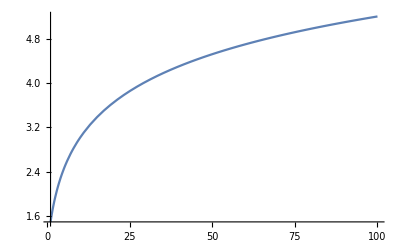

```mathematica
Plot[f[x],{x,1,100}]
```

```mathematica
(*4*)
ClearAll;
```

```mathematica
Limit[Sum[1/i,{i,1,k}]/Log[k],k->Infinity]
```

1

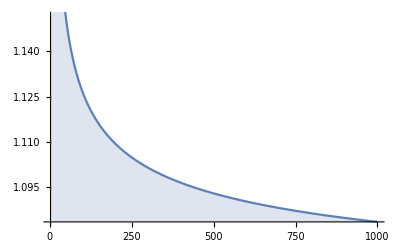

```mathematica
DiscretePlot[Sum[1/i,{i,1,k}]/Log[k],{k,2,1000}]
```

```mathematica
(*5*)
ClearAll;
```

```mathematica
A[z_,u_,x_,y_,k]=1/2(z^2+u^2)+1/4(x+y)^2+1/4(x-k y)^4
B[z_,u_,x_,y_]=(z+u)^2+(x+y)^2
```

1/4 (x+y)^2+1/4 (x-k y)^4+1/2 (u^2+z^2)

(x+y)^2+(u+z)^2

```mathematica
FullSimplify[Solve[D[A[z,u,x,y,k],x] D[B[z,u,x,y],z]-D[A[z,u,x,y,k],z] D[B[z,u,x,y],x]+D[A[z,u,x,y,k],y] D[B[z,u,x,y],u]-D[A[z,u,x,y,k],u] D[B[z,u,x,y],y]==0,k]]
```

{{k→1},{k→x/y},{k→x/y},{k→x/y}}

```mathematica
FullSimplify[D[A[z,u,x,y,k],x] D[B[z,u,x,y],z]-D[A[z,u,x,y,k],z] D[B[z,u,x,y],x]+D[A[z,u,x,y,k],y] D[B[z,u,x,y],u]-D[A[z,u,x,y,k],u] D[B[z,u,x,y],y]]
```

2 (-1+k) (-x+k y)^3 (u+z)

```mathematica
(*6*)
ClearAll;
```

```mathematica
f[x_]=Piecewise[{{Exp[x],x<0},{(x+1)^2,x≥0}}]
```

Piecewise[{{ⅇ^x, x<0}, {(1+x)^2, x≥0}, {0, True}}]

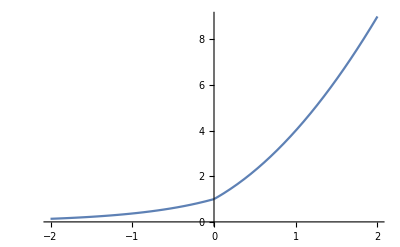

```mathematica
Plot[f[x],{x,-2,2}]
```

```mathematica
(*H sunarthsh einai sunexhs sto x=0*)
```

```mathematica
df[x_]=D[f[x],x]
```

Piecewise[{{ⅇ^x, x<0}, {2 (1+x), x>0}, {Indeterminate, True}}]

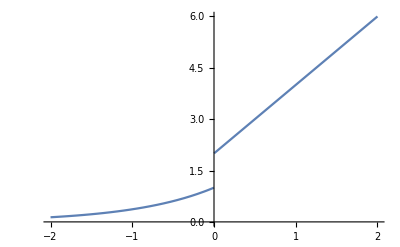

```mathematica
Plot[df[x],{x,-2,2}]
```

```mathematica
(*H sunarthsh den einia paragogisimh sto x=0*)
```

```mathematica
(*7*)
ClearAll;
```

```mathematica
r[k_]:=Sum[RandomChoice[{-1,1}],{i,1,k}]
```

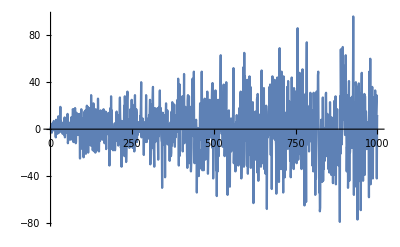

```mathematica
DiscretePlot[r[x],{x,1,1000}]
```

```mathematica
(*8*)
ClearAll;
```

```mathematica
x[k_]:=x[k]=Mod[(51 x[k-1]+1),100]
```

```mathematica
x[0]=RandomInteger[{0,100}]
```

75

```mathematica
Table[x[k],{k,1,100}]
```

{26,27,78,79,30,31,82,83,34,35,86,87,38,39,90,91,42,43,94,95,46,47,98,99,50,51,2,3,54,55,6,7,58,59,10,11,62,63,14,15,66,67,18,19,70,71,22,23,74,75,26,27,78,79,30,31,82,83,34,35,86,87,38,39,90,91,42,43,94,95,46,47,98,99,50,51,2,3,54,55,6,7,58,59,10,11,62,63,14,15,66,67,18,19,70,71,22,23,74,75}

```mathematica
(*9*)
ClearAll;
```

```mathematica
DeleteCases[Table[If[Sum[Divisors[k][[i]],{i,1,Length[Divisors[k]]-1}]==k,k],{k,1,1000}],Null]
```

{6,28,496}

```mathematica
(*10*)
ClearAll;
```

```mathematica
A={"PAOK","OSFP","AEK","ARIS","AEL","OFH"}
```

{PAOK,OSFP,AEK,ARIS,AEL,OFH}

```mathematica
(*Simple way*)
```

```mathematica
B=DeleteDuplicates[Permutations[A,{2}],Sort[#1]==Sort[#2] &]
```

{{PAOK,OSFP},{PAOK,AEK},{PAOK,ARIS},{PAOK,AEL},{PAOK,OFH},{OSFP,AEK},{OSFP,ARIS},{OSFP,AEL},{OSFP,OFH},{AEK,ARIS},{AEK,AEL},{AEK,OFH},{ARIS,AEL},{ARIS,OFH},{AEL,OFH}}

```mathematica
(*NOT so Simple way*)
```

```mathematica
Table[C1=Append[RotateRight[Most[A],i],A[[6]]];{{Part[C1,1],Part[C1,6]},{Part[C1,2],Part[C1,5]},{Part[C1,3],Part[C1,4]}},{i,0,4}]
```

{{{PAOK,OFH},{OSFP,AEL},{AEK,ARIS}},{{AEL,OFH},{PAOK,ARIS},{OSFP,AEK}},{{ARIS,OFH},{AEL,AEK},{PAOK,OSFP}},{{AEK,OFH},{ARIS,OSFP},{AEL,PAOK}},{{OSFP,OFH},{AEK,PAOK},{ARIS,AEL}}}

```mathematica
(*11*)
ClearAll;
```

```mathematica
A={{1,1},{3,4},{-2,5},{2,7},{5,-2},{-1,4}}
```

{{1,1},{3,4},{-2,5},{2,7},{5,-2},{-1,4}}

```mathematica
B={{0,3},{-2,3},{1,3},{2,5},{4,1},{3,1}}
```

{{0,3},{-2,3},{1,3},{2,5},{4,1},{3,1}}

```mathematica
f[i_,j_]:=Sqrt[(Part[A,i,1]-Part[B,j,1])^2+(Part[A,i,2]-Part[B,j,2])^2]
```

```mathematica
data=N[Table[f[i,j],{i,1,6},{j,1,6}]];
```

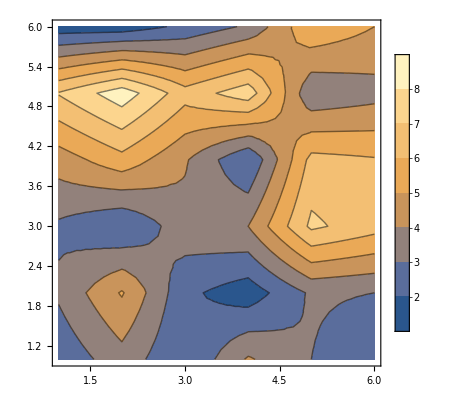

```mathematica
ListContourPlot[data,InterpolationOrder->1,PlotLegends->Automatic]
```

```mathematica
Position[data,N[Min[data]]]
```

{{2,4},{6,1},{6,2}}

```mathematica
(*12*)
ClearAll;
```

```mathematica
f[x_]=y[x]/.DSolve[{y''[x]+1/4 y'[x]+2 y[x]==Sin[x]+Sin[2 x],y[0]==1,y'[0]==0},y,x][[1]]//FullSimplify
```

-2/17 (2 Cos[x]+Cos[2 x]+8 (-1+Cos[x]) Sin[x])+(23 ⅇ^(-x/8) (127 Cos[(√127 x)/8]+√127 Sin[(√127 x)/8]))/2159

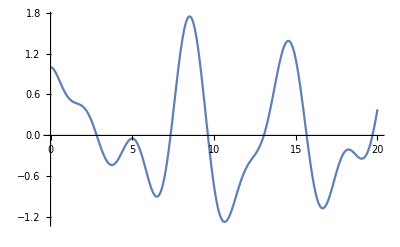

```mathematica
Plot[f[t],{t,0,20}]
```

```mathematica
(*13*)
ClearAll;
```

```mathematica
f[x_]=7/2 x (1-x)
```

7/2 (1-x) x

```mathematica
g[x_]=f[f[f[x]]]//FullSimplify
```

-343/128 (-1+x) x (2+7 (-1+x) x) (8+49 (-1+x) x (2+7 (-1+x) x))

```mathematica
N[Solve[g[x]==0,x]//FullSimplify]
```

{{x→0.},{x→1.},{x→0.5-0.188982 ⅈ},{x→0.5+0.188982 ⅈ},{x→0.163012+0.0801139 ⅈ},{x→0.836988-0.0801139 ⅈ},{x→0.163012-0.0801139 ⅈ},{x→0.836988+0.0801139 ⅈ}}

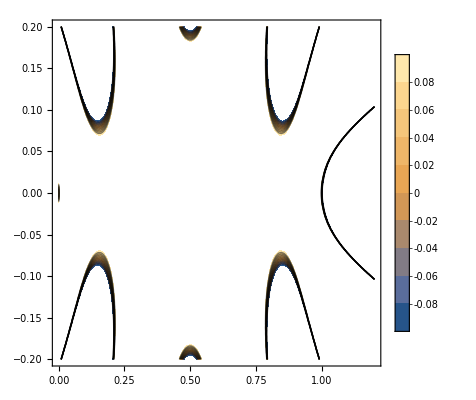
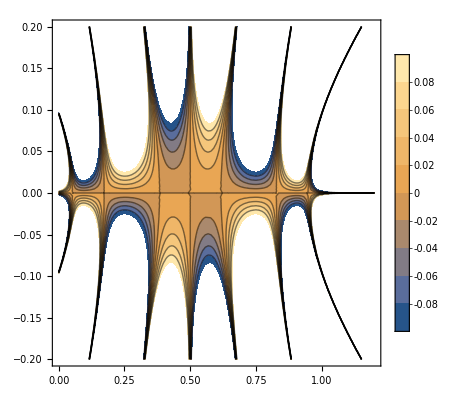

```mathematica
{ContourPlot[Re[g[x+y I]],{x,0,1.2},{y,-0.2,0.2},PlotLegends->Automatic,PlotRange->{-0.1,0.1}],ContourPlot[Im[g[x+y I]],{x,0,1.2},{y,-0.2,0.2},PlotLegends->Automatic,PlotRange->{-0.1,0.1}]}
```

```mathematica
(*14*)
ClearAll;
```

```mathematica
f[x_]=Exp[x^2-x]-x^2
```

ⅇ^(-x+x^2)-x^2

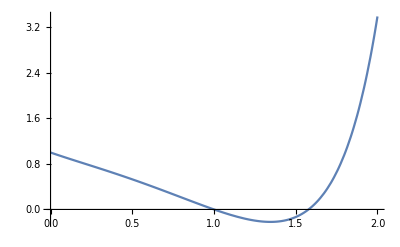

```mathematica
Plot[f[x],{x,0,2}]
```

```mathematica
N[Solve[f[x]==0,x,Reals]//FullSimplify]
```

{{x→1.},{x→1.57826}}

```mathematica
(*15*)
ClearAll;
```

```mathematica
eq1=x-y^2+z==0
eq2=x^2-y-z==1
eq3[k_]:=x y-z^k==-1
```

x-y^2+z==0

x^2-y-z==1

```mathematica
N[Solve[{eq1,eq2,eq3[1]},{x,y,z}]//FullSimplify]
```

{{x→-1.5,y→-0.5,z→1.75},{x→-1.61803,y→-1.,z→2.61803},{x→0.618034,y→-1.,z→0.381966}}

```mathematica
N[Solve[{eq1,eq2,eq3[2]},{x,y,z}]//FullSimplify]
```

{{x→0.661362,y→-1.09056,z→0.527962},{x→2.39233,y→2.21396,z→2.50929},{x→-1.38593-0.0847885 ⅈ,y→-0.348341+0.495299 ⅈ,z→1.26195-0.260277 ⅈ},{x→-1.38593+0.0847885 ⅈ,y→-0.348341-0.495299 ⅈ,z→1.26195+0.260277 ⅈ},{x→-0.704951-1.2939 ⅈ,y→-0.337362+1.63053 ⅈ,z→-1.83987+0.193745 ⅈ},{x→-0.704951+1.2939 ⅈ,y→-0.337362-1.63053 ⅈ,z→-1.83987-0.193745 ⅈ},{x→0.564033-0.367201 ⅈ,y→0.124003-0.62614 ⅈ,z→-0.940707+0.211914 ⅈ},{x→0.564033+0.367201 ⅈ,y→0.124003+0.62614 ⅈ,z→-0.940707-0.211914 ⅈ}}

```mathematica
(*16*)
ClearAll;
```

```mathematica
eq1=x^2+y^2==4;
eq2=Sin[2 x]+Cos[3 y]==1;
eq3=0≤x≤Pi;(*Kanonika einai mexri PI/2 giati allios den orizetai h eq2 alla telos panton*)
eq4=0≤y≤Pi;
```

```mathematica
ans1=NSolve[{eq1,eq2,eq3,eq4},{x,y}]
```

{{x→0.0199619,y→1.9999},{x→1.13234,y→1.64858}}

```mathematica
fig1=ContourPlot[{x^2+y^2==4,Sin[2 x]+Cos[3 y]==1},{x,0,Pi},{y,0,Pi}];
```

```mathematica
fig2=ListPlot[{{x/.ans1[[1]],y/.ans1[[1]]},{x/.ans1[[2]],y/.ans1[[2]]}},PlotStyle->(Red)];
```

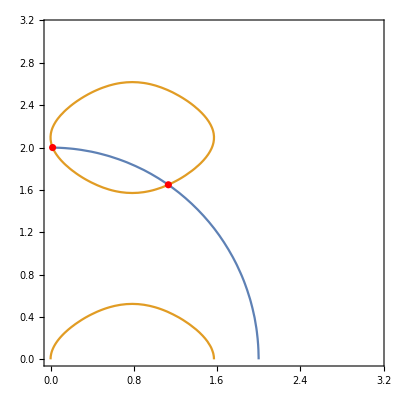

```mathematica
Show[fig1,fig2]
```